# helper

```mathematica
getBlack[s_]:=StringCases[s,("B<< Monte-Carlo "~~Shortest[__]~~" total games: "~~(x:DigitCharacter..)~~WordBoundary):>ToExpression[x]/10^6];
getWhite[s_]:=StringCases[s,("W<< Monte-Carlo "~~Shortest[__]~~" total games: "~~(x:DigitCharacter..)~~WordBoundary):>ToExpression[x]/10^6]
```

```mathematica
ClearAll[makePlot];
makePlot[expr_->data_]:=
Module[{all},
all=Join[getBlack[data],getWhite[data]];
all=all;ListLinePlot[{Legended[Style[Take[all,Length[getBlack[data]]],Black],Placed["Black",Below]],Legended[Style[Drop[all,Length[getBlack[data]]],LightGray],Placed["White",Below]]},PlotLabel->StringTrim[expr,"\\"]];
ListLinePlot[{getWhite[data],getBlack[data]},Mesh->All,PlotLabel->Style[StringTrim[expr,"\\"],Medium],PlotRange->All,PlotMarkers->{Automatic,8},ImageSize->Scaled[0.18],PlotStyle->{LightGray,Black}]]
```

```mathematica
?PlotMarkers
```

PlotMarkers is an option for graphics functions like ListPlot and ListLinePlot that specifies what markers to draw at the points plotted.

## MPI

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata=Map[FileNameSplit[#][[2]]->Import[#,"Text"]&,FileNames["MPI*/gtg_output.txt","mpi"]];
```

```mathematica
data=Normal@Map[Function[{val},StringJoin[Last/@val]],GroupBy[rawdata,StringJoin[Riffle[Most[StringSplit[First[#],"_"]]," "]]&]];
```

```mathematica
Length[data]
```

10

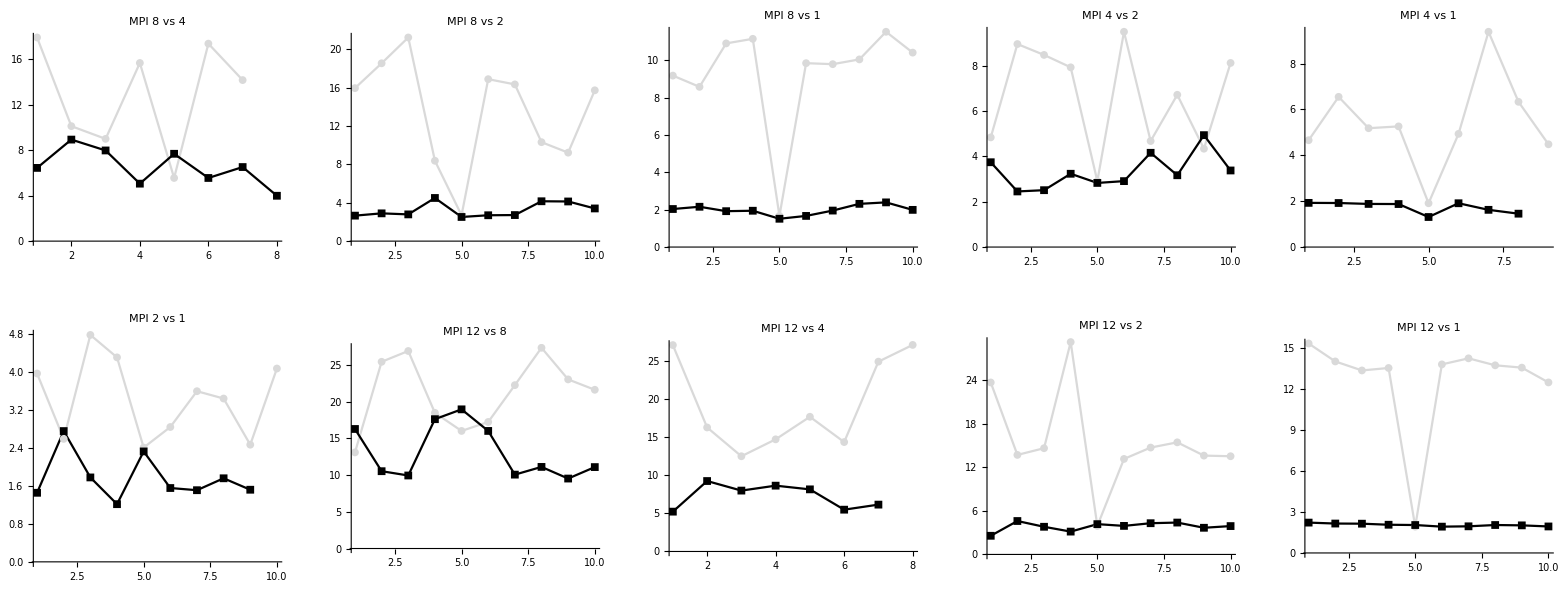

```mathematica
GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],5],ImageSize->Scaled[1],ImagePadding->Scaled[0.1]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"war_MPI_vs.pdf"}],GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],5],ImageSize->Scaled[2],ImagePadding->Scaled[0.2]]]
```

C:\Users\adakk\Desktop\mpi_omp\cs484-master\data\war_MPI_vs.pdf

## OMP

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata=Map[FileNameSplit[#][[2]]->Import[#,"Text"]&,FileNames["OMP*/gtg_output.txt","omp"]];
Length[rawdata]
```

18

```mathematica
data=Normal@Map[Function[{val},StringJoin[Last/@val]],GroupBy[rawdata,StringJoin[Riffle[Most[StringSplit[First[#],"_"]]," "]]&]];
Length[data]
```

9

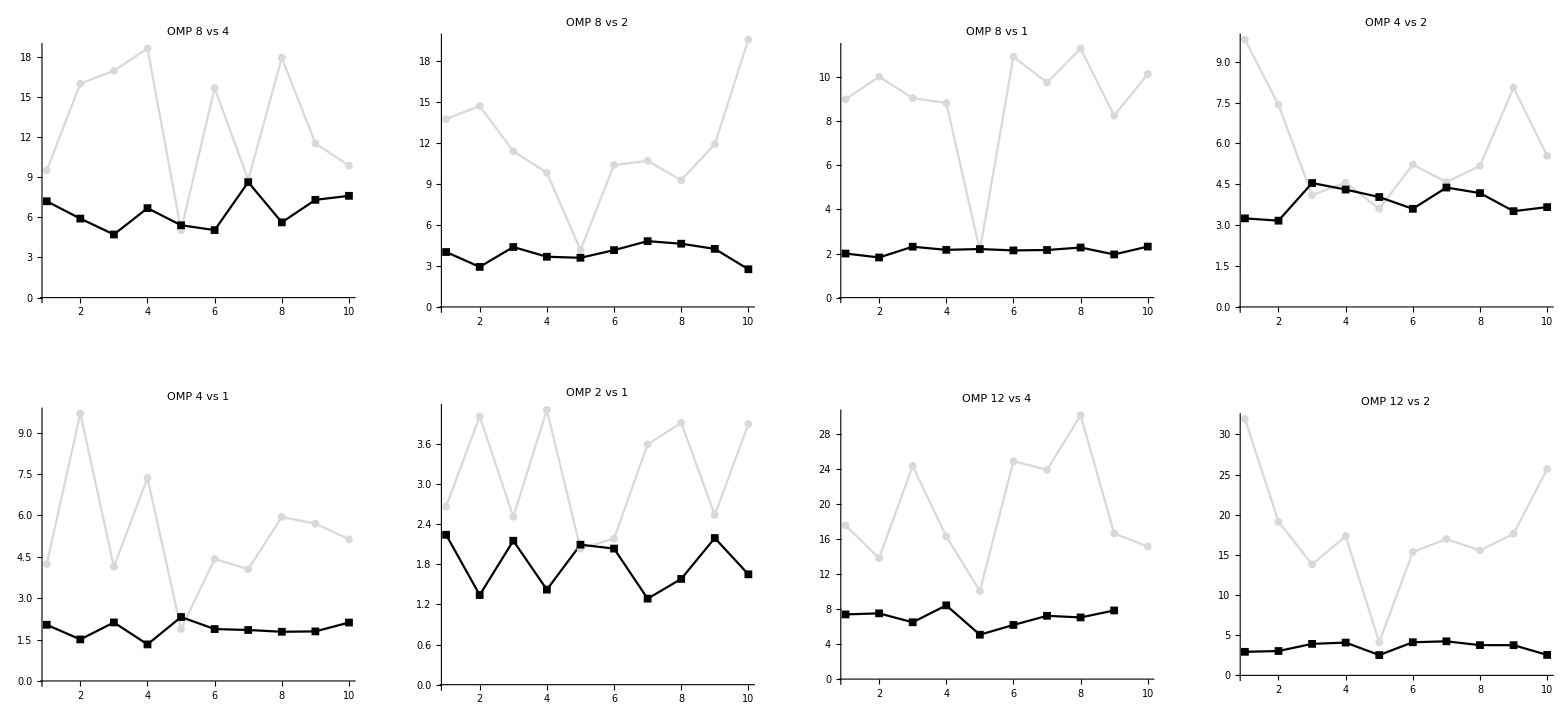

```mathematica
GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],4],ImageSize->Scaled[1]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"war_OMP_vs.pdf"}],GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],4],ImageSize->Scaled[2],ImagePadding->Scaled[0.2]]]
```

C:\Users\adakk\Desktop\mpi_omp\cs484-master\data\war_OMP_vs.pdf

## MPI/OMP

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata=Map[FileNameSplit[#][[2]]->Import[#,"Text"]&,FileNames["MPI*/gtg_output.txt","mpi_omp"]];
Length[rawdata]
```

16

```mathematica
data=Normal@Map[Function[{val},StringJoin[Last/@val]],GroupBy[rawdata,StringJoin[Riffle[Most[StringSplit[First[#],"_"]]," "]]&]];
Length[data]
```

8

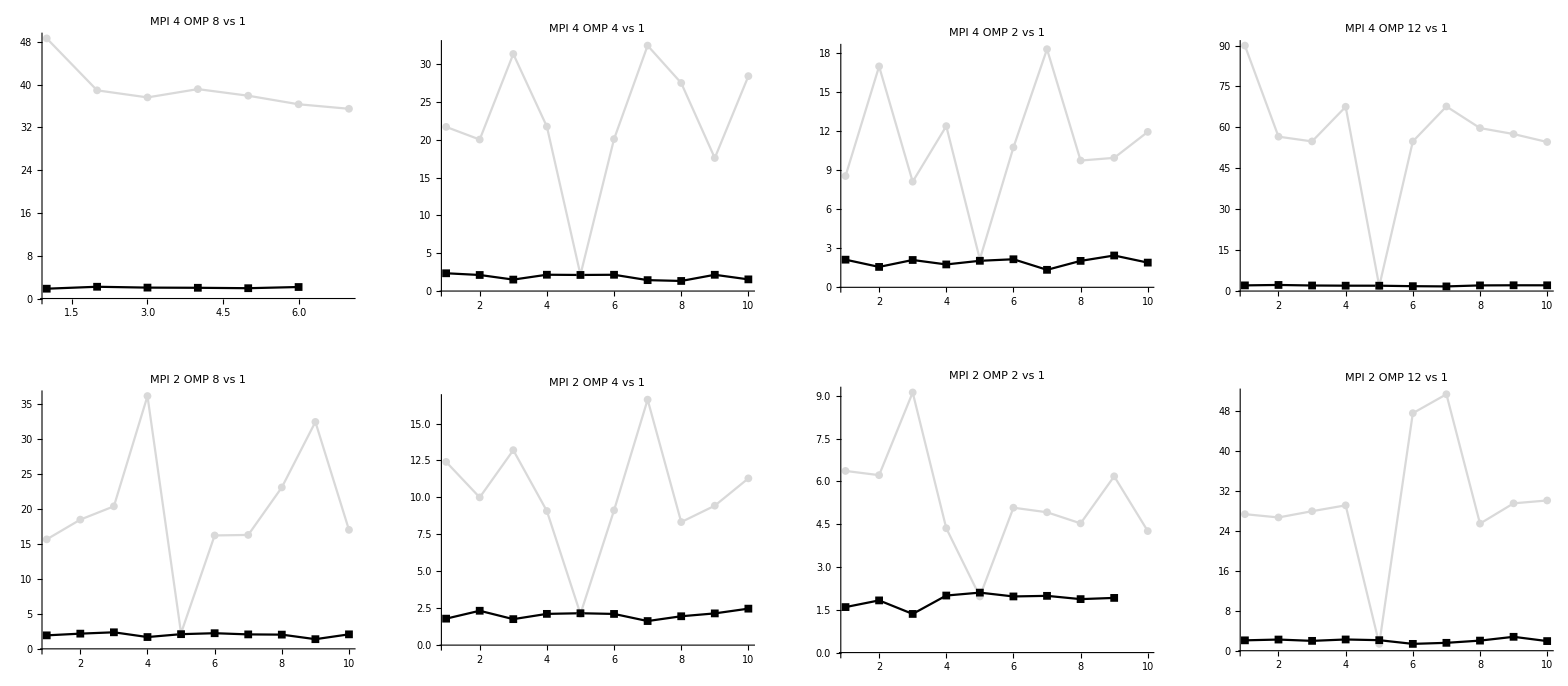

```mathematica
GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],4],ImageSize->Scaled[1],ImagePadding->Scaled[0.1]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"war_MPI_OMP_vs.pdf"}],GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],4],ImageSize->Scaled[2],ImagePadding->Scaled[0.2]]]
```

C:\Users\adakk\Desktop\mpi_omp\cs484-master\data\war_MPI_OMP_vs.pdf